```mathematica
wpe[n_]:=Sqrt[n q^2/(m ϵ0)];
(*wce[Z_]:=Abs[Z] q b0 /m;*)
ζ[vTh_,k_,ω_]:=ω/(k vTh);
Z[x_]:= I Sqrt[Pi] Exp[-x^2] Erfc[-I x];
(*Z[x_]:= I Sqrt[Pi] Exp[-x^2] (1+Erfi[-I x/I]/I);*)
Zp[x_]:=-2 (1+x Z[x]);
K3[vTh_,k_,ω_,n_]=FullSimplify[1-wpe[n]^2/(ω k vTh) Sum[BesselI[b,0] ζ[vTh,k,ω] Zp[ζ[vTh,k,ω]],{b,0,0}]];
sig33[vTh_,ω_,k_,n_]=Simplify[-(K3[vTh,k,ω,n]-1) I ω ϵ0]
stixP[n_]:=1-wpe[n]^2/ω^2;
sig33Cold[n_]:=-(stixP[n]-1) I ω ϵ0
```

-(2 ⅈ n q^2 ω (k vTh+ⅈ ⅇ^(-ω^2/(k^2 vTh^2)) √π ω Erfc[-(ⅈ ω)/(k vTh)]))/(k^3 m vTh^3)

```mathematica
x[v_,t_]:=v t;
eField[v_,t_,E0_]:= E0 Exp[-I (k x[v,t]+ω t )];
v1[v_,nRF_,rfPeriod_,E0_]=q/m Integrate[eField[v,t,E0],{t,-nRF rfPeriod,0}]
v1Indef[v_,E0_]=q/m Integrate[eField[v,t,E0],{t,-Infinity,0},Assumptions->{k∈Reals,v∈Reals,Im[ω]>0}]
f[v_,vTh_,n_]:= n/(vTh Sqrt[Pi]) Exp[-v^2/vTh^2];
f1[v_,vTh_,n_,nRF_,rfPeriod_,E0_]:=-v1[v,nRF,rfPeriod,E0] D[f[v,vTh,n],v];
f1Indef[v_,vTh_,n_,E0_]:=-v1Indef [v,E0]D[f[v,vTh,n],v];
j[n_,vTh_,nRF_,rfPeriod_,E0_]:=q NIntegrate[ v f1[v,vTh,n,nRF,rfPeriod,E0],{v,-5 vTh,5 vTh}]
jIndef[n_,vTh_,E0_]=q Integrate[v f1Indef[v,vTh,n,E0],{v,-Infinity,Infinity},Assumptions->{k∈Reals,v∈Reals,Im[ω]>0,Re[ω]>0,vTh∈Reals,vTh>0,Abs[k]>0}]
sig33Dlg=FullSimplify[jIndef[n,vTh,1],Assumptions->{Im[k/ω]>0}]
```

-(ⅈ (-1+ⅇ^(ⅈ nRF rfPeriod (k v+ω))) E0 q)/(m (k v+ω))

(ⅈ E0 q)/(m (k v+ω))

(2 ⅈ E0 n q^2 ω (-k √π vTh+ⅇ^(-ω^2/(k^2 vTh^2)) ω (π Erfi[ω/(k vTh)]-Log[-k/ω]+Log[k/ω])))/(k^3 m √π vTh^3)

-(2 n q^2 ω (ⅈ k vTh+ⅇ^(-ω^2/(k^2 vTh^2)) √π ω-2 ⅈ ω DawsonF[ω/(k vTh)]))/(k^3 m vTh^3)

```mathematica
sig33[vTh,ω,ϵ0,k,n,m,q]
FullSimplify[ sig33Dlg/sig33[vTh,ω,ϵ0,k,n,m,q],,Assumptions->{k∈Reals,v∈Reals,Im[ω]>0,Re[ω]>0,vTh∈Reals,vTh>0,Abs[k]>0,Im[k/ω]>0}]
```

sig33[vTh,ω,ϵ0,k,n,m,q]

-(2 n q^2 ω (ⅈ k vTh+ⅇ^(-ω^2/(k^2 vTh^2)) √π ω-2 ⅈ ω DawsonF[ω/(k vTh)]))/(k^3 m vTh^3 sig33[vTh,ω,ϵ0,k,n,m,q])

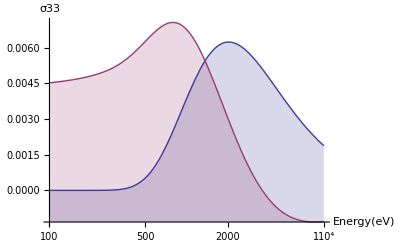

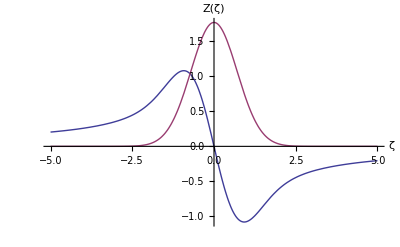

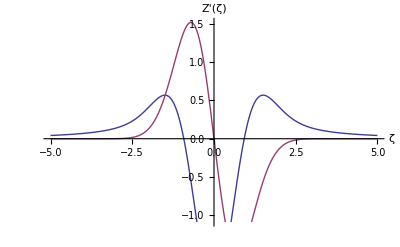

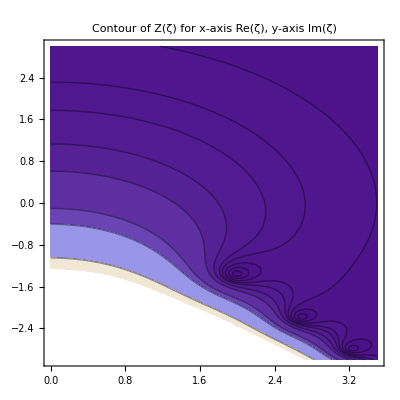

{{100,5.03071×10^-9},{200,2.35742×10^-7},{300,0.0000197117},{500,0.000524698},{800,0.00252735},{1000,0.00386321},{1500,0.00578551},{2000,0.00623303},{3000,0.00562766},{4000,0.00470763},{5000,0.00392073},{6000,0.00330026},{7000,0.00281529},{10000,0.00187794}}

```mathematica
eCharge=1.60217646 10^-19; m=9.10938188 10^-31;
q=-eCharge;
freq=1.15 10^8;
E0=5000;
rfPeriod=1/freq;
vTh[someeV_]:=Sqrt[2 someeV eCharge/m];
n=1.1 10^14;
k = 22.11;
nRF =5;
ω=2 Pi freq +I 2 Pi freq 1 10^-6;
vPhs=Re[ω/k];tPhs=0.5 m vPhs^2/eCharge;
kPer=0;
vPhs=w/kPar;
λ=2 Pi /kPar;
ϵ0=8.854187817 10^-12;

LogLinearPlot[{Re[sig33[vTh[EeV],ω,k,n]],Im[sig33[vTh[EeV],ω,k,n]]},{EeV,100,10000},Filling->Axis,AxesLabel->{Energy [eV],σ33}]
Plot[{Re[Z[x]],Im[Z[x]]},{x,-5,5},AxesLabel->{"ζ","Z(ζ)"}]
Plot[{Re[Zp[x]],Im[Zp[x]]},{x,-5,5},AxesLabel->{"ζ","Z'(ζ)"}]
ContourPlot[Abs[Z[x+I y]],{x,0,3.5},{y,-3.0,3.0},Contours->{0.1,0.2,0.3,0.4,0.5,0.7,1.0,2.0,3.0,10.0,100.0},PlotLabel->"Contour of Z(ζ) for x-axis Re(ζ), y-axis Im(ζ)"]
tValsZ={100,200,300,500,800,1000,1500,2000,3000,4000,5000,6000,7000,10000};
reValsZ= Table[{rteV,Re[sig33[vTh[rteV],ω,k,n]]},{rteV,tValsZ}]
imValsZ= Table[{rteV,Im[sig33[vTh[rteV],ω,k,n]]},{rteV,tValsZ}];
```

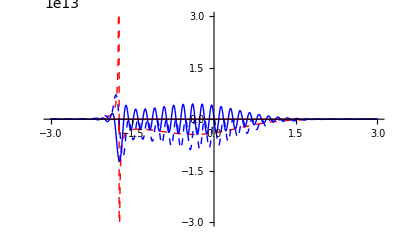

```mathematica
thiseV=1000;
thisnRF=10;
Plot[{Re[v1Indef[v vTh[thiseV],E0]f[v vTh[thiseV],vTh[thiseV],n]] ,
Im[v1Indef[v vTh[thiseV],E0]f[v vTh[thiseV],vTh[thiseV],n]],
Re[v1[v vTh[thiseV],thisnRF,rfPeriod,E0]f[v vTh[thiseV],vTh[thiseV],n]],Im[v1[v vTh[thiseV],thisnRF,rfPeriod,E0]f[v vTh[thiseV],vTh[thiseV],n]]},{v,-3 ,3},PlotStyle->{Directive[Red,Thick],Directive[Red,Dashed,Thick],Blue,Directive[Blue,Dashed]},PlotRange->0.3 10^14]
```

```mathematica
NIntegrate[  f[v,vTh[500],n],{v,-3 vTh[500],3 vTh[500]}]
```

1.09998×10^14

```mathematica
thiseV=100;
j[n,vTh[thiseV],10,rfPeriod,E0]
jIndef[n,vTh[thiseV],E0]
```

-0.000025159-22.6083 ⅈ

-0.0000251536-22.6083 ⅈ

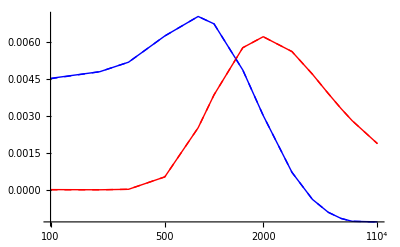

```mathematica
tVals={100,200,300,500,800,1000,1500,2000,3000,4000,5000,6000,7000,10000};
thisnRF =5;

reVals= Table[{rteV,
Re[j[n,vTh[rteV],thisnRF,rfPeriod,E0]/eField[0,0,E0] ]},{rteV,tVals}];
imVals=Table[{rteV,
Im[j[n,vTh[rteV],thisnRF,rfPeriod,E0]/eField[0,0,E0]]},{rteV,tVals}];
ListLogLinearPlot[{reVals,imVals,reValsZ,imValsZ},PlotStyle->{Red,Blue,Directive[Red,Dashed],Directive[Blue,Dashed]},Joined->True]
```